```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
(**************************************)
```

```mathematica
dateMouseSessionListV1toV2m={{"101620","Mouse23392","Session2"},{"102120","Mouse23392","Session1"},{"102520","Mouse23392","Session1"},{"101520","Mouse23393","Session1"},{"101420","Mouse23395","Session1"},{"121320","Mouse23379","Session2"},{"121620","Mouse23379","Session2"},{"122020","Mouse23379","Session1"},{"121820","Mouse23365","Session2"},{"122120","Mouse23365","Session1"},{"020521","Mouse23320","Session1"},{"021321","Mouse23329","Session1"},{"030121","Mouse23329","Session1"},{"030621","Mouse23329","Session2"}};
```

```mathematica
dateMouseSessionListLPtoV2m={{"101720","Mouse23394","Session2"},{"101920","Mouse23394","Session1"},{"102020","Mouse23394","Session1"},{"102220","Mouse23394","Session3"},{"100820","Mouse23399","Session1"},{"101020","Mouse23399","Session1"},{"102320","Mouse23399","Session1"},{"102920","Mouse23377","Session2"},{"102920","Mouse23394","Session2"},{"110120","Mouse23394","Session1"},{"110320","Mouse23394","Session2"},{"103120","Mouse23377","Session2"},{"110220","Mouse23377","Session2"},{"103120","Mouse23378","Session1"},{"110220","Mouse23378","Session1"},{"111520","Mouse23384","Session2"},{"111720","Mouse23384","Session1"},{"111820","Mouse23384","Session2"},{"112120","Mouse23384","Session1"},{"120320","Mouse23378","Session2"},{"120220","Mouse23378","Session1"},{"120320","Mouse23384","Session2"},{"120220","Mouse23384","Session1"},{"121620","Mouse23381","Session1"},{"121820","Mouse23381","Session1"},{"011121","Mouse23369","Session2"},{"011521","Mouse23369","Session1"},{"010621","Mouse23339","Session1"},{"010821","Mouse23339","Session1"},{"011421","Mouse23339","Session2"},{"062922","Mouse23067","Session2"},{"070122","Mouse23075","Session1"},{"070822","Mouse23075","Session2"}};
```

```mathematica
dateMouseSessionListLMtoV2m={{"092321","Mouse22422","Session1"},{"100521","Mouse22422","Session1"},{"081621","Mouse22437","Session2"},{"081821","Mouse22437","Session1"},{"082421","Mouse22437","Session2"},{"092421","Mouse22472","Session1"},{"101121","Mouse22472","Session2"},{"102121","Mouse22422","Session2"},{"102021","Mouse22436","Session1"},{"102121","Mouse22436","Session2"},{"102821","Mouse22472","Session1"},{"071322","Mouse23100","Session1"},{"071022","Mouse23014","Session1"},{"070822","Mouse22518","Session2"},{"071222","Mouse22518","Session1"}};
```

```mathematica
(**************)
```

```mathematica
randDotCorrValsV1toV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/V1toV2m/ValuesForPlotting/motionCoherCorrVals_V1toV2m_nonDupROIs.txt","List"]];
```

```mathematica
randDotCorrValsLPtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LPtoV2m/ValuesForPlotting/motionCoherCorrVals_LPtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
randDotCorrValsLMtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LMtoV2m/ValuesForPlotting/motionCoherCorrVals_LMtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
randDotCorrValsV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/motionCoherCorrVals_V2m.txt","List"]];
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[randDotCorrValsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[randDotCorrValsV1toV2m,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[randDotCorrValsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[randDotCorrValsLMtoV2m,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[randDotCorrValsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[randDotCorrValsLPtoV2m,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[randDotCorrValsLPtoV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-1,1}},ChartStyle->Transparent,Frame->False],DistributionChart[randDotCorrValsLPtoV2m,PlotRange->{All,{-1,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-1,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

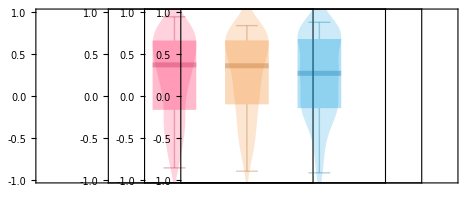

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-400}}]
```